# Import J from cs_dump2

Verifying/tuning the conjugate gradient (Krylov subspace) solver.

```mathematica
$base=NotebookDirectory[]~FileNameJoin~"s3d132 partition 0 of 27";
$j=Import[$base~FileNameJoin~"J2.txt","Table"];
$b=1.Flatten@Rest@Import[$base~FileNameJoin~"minusFx.txt","Table"];

$js=$j//First;

$jd=($j//Rest(*extra rest: skip NNZ, can be inferred*)//Rest);
$jd=Function[{i,j,x},{i,j}+1->1.x]@@@$jd;

$jm=SparseArray[$jd,$js,0.];
Dimensions@$jm
Dimensions@$b

$sol=LeastSquares[$jm,$b,Method->"Krylov"]
```

{5632,1024}

{5632}

{0.00171268,0.0000709457,-0.0438457,0.0000787778,-0.0674701,0.0000755787,-0.0757529,0.0000701318,-0.0776215,0.0000649662,-0.0769125,0.0000611262,-0.0735974,0.0000592526,-0.0572033,0.0000654256,0.00388195,0.000131442,-0.017887,0.000126409,-0.032476,0.000117664,-0.0386516,0.000107341,-0.0403819,0.0000979224,-0.0400866,0.0000908684,-0.0380724,0.0000870954,-0.0269895,0.0000899684,0.00550343,0.000192463,-0.000588325,0.000184375,-0.0058273,0.000173372,-0.00855277,0.000161418,-0.00956416,0.000150542,-0.00969935,0.00014222,-0.00924582,0.000137446,-0.00238562,0.000136606,0.00681419,0.000249035,0.00260444,0.000242872,-0.000016966,0.000232834,-0.00128016,0.000221842,-0.00188764,0.000211615,-0.00222953,0.000203576,-0.00237785,0.000198884,0.00485696,0.000197216,0.00776865,0.000304624,-0.00178551,0.000302173,-0.00591856,0.000294608,-0.00706613,0.000285773,-0.00744966,0.000277192,-0.00775173,0.000270243,-0.00781434,0.000266397,0.00218107,0.000266221,0.00799567,0.000365983,-0.00774227,0.000372896,-0.0126503,0.000368592,-0.0130187,0.000362214,-0.0127691,0.000355527,-0.01273,0.00034985,-0.0124822,0.000347037,-0.0000391576,0.000349097,0.00524383,0.000391064,-0.00396271,0.00040152,-0.00321244,0.000398674,-0.000679916,0.000394256,0.000783168,0.000389388,0.00131255,0.000384875,0.00165893,0.000382287,0.012249,0.000380212,0.00129315,0.000350168,0.0123332,0.000326952,0.0223924,0.000322101,0.0277151,0.000318888,0.0298786,0.000315462,0.0305623,0.000311907,0.0306835,0.000308807,0.0354934,0.000297097,-0.0465228,0.0000754999,-0.0669016,0.00140126,-0.0709658,0.00207461,-0.0694134,0.00230129,-0.0662402,0.00234335,-0.0602147,0.00231332,-0.0425709,0.00220596,0.0248508,0.00181229,-0.0211795,0.000141643,-0.0363716,0.00083375,-0.0385575,0.00128588,-0.0371214,0.00146257,-0.0346473,0.00149694,-0.0301928,0.00147001,-0.0188611,0.00139071,0.0185892,0.00112909,-0.0046426,0.000210353,-0.0122592,0.000401519,-0.0122527,0.000555279,-0.0109658,0.000621095,-0.00951693,0.000630464,-0.00722418,0.000614706,-0.00204186,0.000585694,0.0140034,0.000489789,-0.00292118,0.000269884,-0.00681246,0.00040699,-0.00530306,0.000478584,-0.00380464,0.000499367,-0.00276257,0.000497602,-0.0013042,0.000489854,0.00247589,0.000482046,0.0160558,0.000424145,-0.0102202,0.000325876,-0.0116856,0.000674876,-0.00770714,0.000812691,-0.00496642,0.000836777,-0.00353271,0.00083195,-0.00193903,0.000825875,0.00291568,0.000816065,0.0231261,0.000713101,-0.0218993,0.000395843,-0.0163669,0.0010496,-0.00737666,0.00124131,-0.00222421,0.00124363,0.000151963,0.00121901,0.00206334,0.00120301,0.00742137,0.00118141,0.0320371,0.00102855,-0.0219723,0.000540988,-0.0085564,0.000961475,0.00599922,0.000925505,0.0136738,0.00080843,0.0169261,0.000735391,0.0186585,0.000701545,0.0213917,0.00068002,0.0332827,0.0005975,-0.0108628,0.000698548,0.0119081,0.000212615,0.0293084,-0.000201669,0.0373546,-0.000422293,0.0403996,-0.000516366,0.041278,-0.000551609,0.0395341,-0.0005544,0.025679,-0.000479612,-0.100189,0.000142993,-0.0790746,0.00269536,-0.0440861,0.00392118,-0.0241584,0.00427787,-0.013093,0.00429285,-0.00121647,0.00416125,0.0256754,0.00382924,0.10357,0.0029126,-0.0563288,0.000269504,-0.0180324,0.00167719,0.0174001,0.00245831,0.0347203,0.00271482,0.0435967,0.0027175,0.0516147,0.00259013,0.0640638,0.00232302,0.0912714,0.001722,-0.0245826,0.000386516,0.00497327,0.000858765,0.0286214,0.00108425,0.0387765,0.00114684,0.043658,0.00111854,0.0475839,0.00102884,0.051137,0.000887254,0.0550695,0.000647117,-0.0201539,0.000504148,0.00374871,0.000832735,0.0210068,0.000890094,0.0271777,0.000867496,0.0299267,0.000822866,0.0327317,0.000754887,0.0363274,0.000660359,0.0427215,0.000497378,-0.0312263,0.000674725,-0.00352057,0.00128139,0.0162703,0.00137705,0.0230412,0.00131849,0.0257149,0.00125189,0.0288621,0.00118259,0.0351375,0.00108201,0.0514656,0.000844457,-0.0445375,0.00100687,-0.00404146,0.00189022,0.0233252,0.00190007,0.0328083,0.00171301,0.0361013,0.00157577,0.0392271,0.00148118,0.0457583,0.00136872,0.0654734,0.00109081,-0.0425405,0.00157984,0.0129322,0.00188018,0.0464013,0.00130144,0.0574999,0.000808992,0.0608142,0.000553102,0.062666,0.000428014,0.064101,0.000346373,0.0653115,0.000265566,-0.0137233,0.0023309,0.0511217,0.000874433,0.0820757,-0.000422861,0.0909919,-0.00109047,0.0930695,-0.00136699,0.0929669,-0.00147288,0.0871484,-0.00148635,0.0549985,-0.00126362,-0.157159,0.000577562,0.139432,0.00382681,0.253912,0.00489571,0.288757,0.00500358,0.300497,0.00483376,0.310032,0.00455279,0.32672,0.00402893,0.344675,0.00287085,-0.0466714,0.000927268,0.192218,0.00170943,0.279607,0.00184866,0.303286,0.00177534,0.310448,0.00160161,0.312072,0.00134241,0.298989,0.0010019,0.242714,0.000644661,-0.0129825,0.00111389,0.145243,0.000833806,0.185542,0.00041129,0.190602,0.000201317,0.191167,0.000050661,0.189051,-0.000132646,0.173087,-0.000302595,0.124932,-0.000271269,-0.0165628,0.00136413,0.10605,0.00113181,0.124006,0.000659715,0.119338,0.000427755,0.116745,0.000294569,0.115796,0.000143891,0.108909,-0.000013492,0.0868032,-0.0000653479,-0.0334883,0.00186046,0.0899282,0.00196088,0.107596,0.00148242,0.10181,0.00117393,0.098746,0.00100055,0.0995754,0.0008381,0.100138,0.00063975,0.0967385,0.000411425,-0.0429652,0.00285078,0.100434,0.00300381,0.126275,0.00213408,0.122059,0.00152137,0.11877,0.00120549,0.119544,0.000998196,0.121303,0.000786065,0.122009,0.000529137,-0.0255841,0.0045095,0.148061,0.00345894,0.177929,0.00145714,0.172172,0.000286312,0.167112,-0.000235426,0.165515,-0.00048363,0.160833,-0.000630361,0.139317,-0.000590562,0.0899735,0.00660346,0.25286,0.00259189,0.259085,-0.000483039,0.243483,-0.00187718,0.23478,-0.00240667,0.23004,-0.00260518,0.21673,-0.00263648,0.157639,-0.00223099,0.865516,0.00223757,1.71128,-0.000655417,1.78683,-0.00187598,1.78041,-0.00250738,1.77182,-0.00292418,1.76675,-0.00324943,1.73391,-0.00362512,1.43711,-0.00361291,0.934272,0.00247812,0.92723,-0.00354673,0.855203,-0.00596327,0.821979,-0.00672421,0.808493,-0.00707425,0.789071,-0.00732768,0.708385,-0.00725942,0.439485,-0.00560065,0.926987,0.0028607,0.615744,-0.00237183,0.447465,-0.00433774,0.391328,-0.00481178,0.374318,-0.00498247,0.357027,-0.00513343,0.300598,-0.00500173,0.158962,-0.00366896,0.892149,0.00341618,0.511937,-0.000610163,0.316708,-0.00193174,0.253574,-0.00213657,0.237063,-0.00219257,0.22779,-0.00232329,0.200418,-0.00236812,0.131883,-0.00181291,0.899114,0.00461456,0.510505,0.00108304,0.31178,-0.000158997,0.247206,-0.000409697,0.231199,-0.000502111,0.227019,-0.000669782,0.21523,-0.000866333,0.177011,-0.0008058,0.969985,0.00678896,0.582456,0.00286091,0.378633,0.00088581,0.309315,0.000165028,0.290715,-0.000135105,0.286619,-0.000372342,0.2781,-0.000615061,0.245305,-0.000659214,1.1924,0.0102829,0.77053,0.00428007,0.525272,0.000567396,0.435554,-0.000978536,0.40833,-0.0015778,0.399547,-0.00187328,0.383674,-0.00204248,0.326061,-0.0017898,2.10223,0.0144655,1.21321,0.00429678,0.778618,-0.000896373,0.631903,-0.00280558,0.587594,-0.00345435,0.571366,-0.00369529,0.545188,-0.00373244,0.44826,-0.00315848,0.356949,-0.0151354,-1.63025,-0.0413166,-1.92814,-0.0451549,-1.9764,-0.0459273,-1.99527,-0.0462744,-2.01171,-0.0464553,-2.17633,-0.0463882,-3.58339,-0.042274,-0.432279,-0.0159631,-0.962329,-0.0253823,-1.11736,-0.0274858,-1.15209,-0.0278069,-1.16616,-0.0279359,-1.20228,-0.0279778,-1.36369,-0.0271271,-1.84257,-0.0215094,-0.855941,-0.0161155,-0.832768,-0.0155788,-0.806461,-0.0142245,-0.792951,-0.0134543,-0.790745,-0.0132095,-0.813422,-0.0131568,-0.90163,-0.0125251,-1.07726,-0.00924908,-1.06381,-0.0152133,-0.840057,-0.0108884,-0.703992,-0.0076936,-0.650515,-0.00626393,-0.632299,-0.00580719,-0.638105,-0.00577025,-0.681311,-0.00558436,-0.776857,-0.00418977,-1.17632,-0.0137009,-0.850302,-0.00816396,-0.652111,-0.00457133,-0.575552,-0.00309363,-0.548442,-0.00265853,-0.544792,-0.00268848,-0.568874,-0.00278656,-0.644883,-0.00230491,-1.25671,-0.0116837,-0.821546,-0.00593441,-0.585862,-0.00293798,-0.504442,-0.00193549,-0.478546,-0.00172592,-0.474143,-0.00184274,-0.494378,-0.00203743,-0.569401,-0.00182093,-1.2571,-0.00781646,-0.707362,-0.00366337,-0.47899,-0.00242503,-0.422252,-0.00233761,-0.411209,-0.00247417,-0.414535,-0.00266511,-0.443222,-0.00281336,-0.542568,-0.00243892,-0.774129,-0.00158274,-0.376298,-0.00149226,-0.354923,-0.00248107,-0.398873,-0.00315346,-0.426517,-0.00347874,-0.446059,-0.00365053,-0.488426,-0.00368812,-0.622878,-0.00312823,-0.530262,-0.0110342,-1.26684,-0.0173248,-1.34204,-0.0181377,-1.37411,-0.0184948,-1.39189,-0.0186982,-1.39967,-0.0187961,-1.44213,-0.0188446,-2.30988,-0.0182291,-0.588861,-0.0114875,-1.07779,-0.0164682,-1.18622,-0.0171821,-1.20382,-0.0171417,-1.21138,-0.0171441,-1.23774,-0.0171628,-1.34618,-0.0166438,-1.66793,-0.0132876,-0.816132,-0.0107646,-0.969281,-0.0122828,-0.94287,-0.0114734,-0.906787,-0.0107625,-0.892725,-0.0104948,-0.91029,-0.0104418,-0.985509,-0.00997468,-1.1217,-0.00745721,-0.947753,-0.00866758,-0.917853,-0.00873832,-0.777229,-0.00722832,-0.690819,-0.00622408,-0.655305,-0.00584852,-0.658595,-0.00582037,-0.708247,-0.00566076,-0.816818,-0.0043483,-1.00154,-0.00603578,-0.850459,-0.0058176,-0.635224,-0.00447759,-0.51761,-0.00363101,-0.46944,-0.0033367,-0.464007,-0.0033801,-0.503478,-0.00344867,-0.618386,-0.00285103,-0.964056,-0.0031105,-0.706006,-0.00312818,-0.452294,-0.00252841,-0.331177,-0.00217313,-0.285666,-0.00209817,-0.280778,-0.002223,-0.319453,-0.00238655,-0.439085,-0.00209219,-0.7252,0.000487607,-0.337134,-0.000493726,-0.131722,-0.00118859,-0.0663839,-0.00154466,-0.0506789,-0.00174596,-0.0589593,-0.00193093,-0.105185,-0.00208139,-0.229905,-0.00182355,1.43532,0.00504089,0.899232,0.00138996,0.527487,-0.000694065,0.360596,-0.0015341,0.294302,-0.00185611,0.255611,-0.00201578,0.193727,-0.00208479,0.0593611,-0.00178336,-0.745102,-0.0047849,-0.57159,-0.00389629,-0.616892,-0.00413574,-0.657586,-0.00434007,-0.6821,-0.00446796,-0.694202,-0.00453333,-0.707754,-0.00455483,-1.02732,-0.00449991,-0.814826,-0.00607816,-0.879366,-0.00663087,-0.886097,-0.00655701,-0.887615,-0.00646676,-0.89429,-0.00646754,-0.913361,-0.00650328,-0.968157,-0.00632837,-1.09644,-0.00504224,-0.677679,-0.00452014,-0.845102,-0.00579128,-0.841638,-0.00570249,-0.814336,-0.00544777,-0.803591,-0.00534606,-0.81848,-0.00535065,-0.867817,-0.00516468,-0.93648,-0.00395427,-0.314291,-0.00177224,-0.616889,-0.00378379,-0.654536,-0.00407622,-0.622137,-0.0039123,-0.601546,-0.00382026,-0.611563,-0.00384763,-0.659808,-0.00378417,-0.747995,-0.00300283,0.366246,0.00116695,-0.144645,-0.00152884,-0.295444,-0.00241855,-0.294412,-0.0025295,-0.278929,-0.00253929,-0.290164,-0.00261688,-0.346084,-0.00266463,-0.469681,-0.0022281,1.3759,0.00371328,0.658838,0.000657339,0.32971,-0.000831268,0.248718,-0.0012933,0.23336,-0.0014501,0.210355,-0.00157884,0.144603,-0.00168606,0.00717292,-0.00147496,2.62216,0.0058268,1.94203,0.00260166,1.33891,0.000539946,1.08658,-0.000267865,0.998427,-0.000562586,0.949735,-0.000720807,0.879232,-0.000835433,0.772195,-0.000754463,7.83997,0.00794917,4.86598,0.0034836,3.09814,0.00102296,2.44209,0.000121424,2.22805,-0.000180572,2.14273,-0.000306428,2.0711,-0.000377321,2.0143,-0.000333791}

```mathematica
$h=1.Flatten@Rest@Import[$base~FileNameJoin~"h.txt","Table"];
"maximum error versus Mathematica machine precision solution"
Max[$sol-$h]
```

## minmax

```mathematica
MinMax@$jm
MinMax@$b
MinMax@$sol
```

{-134.433,93.3792}

{-0.615717,0.236539}

{-3.58339,7.83997}

## j spectrum

631

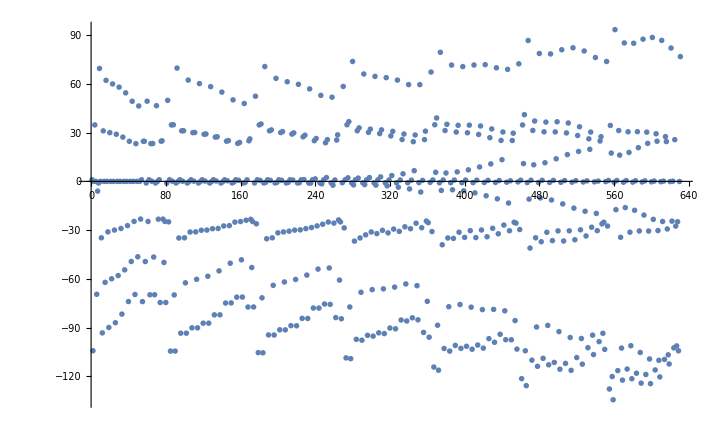

```mathematica
$fjm=DeleteDuplicates@Flatten@$jm;
$fjm//Length
ListPlot[$fjm,PlotRange->Full]
```

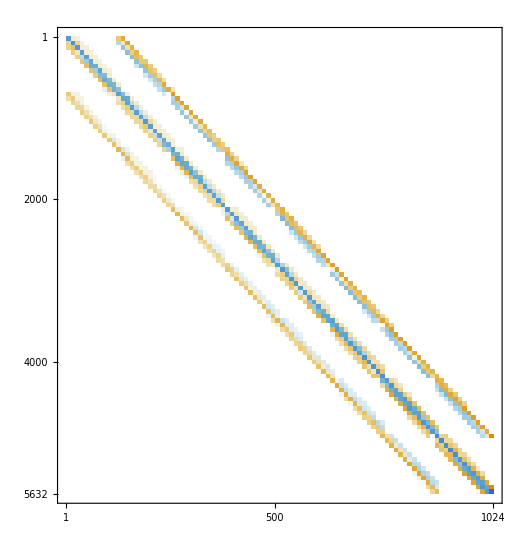

```mathematica
$jm//MatrixPlot
```

```mathematica
$sol2=LeastSquares[SetPrecision[$jm,30],SetPrecision[$b,30],Method->"Krylov"];
"maximum error versus Mathematica high precision solution"
Max[$sol2-SetPrecision[$h,30]]
```